```mathematica
(*Studying SHO Through its Hmiltonian Eq.*)
ω=20;m=1;
```

```mathematica
(*Define Hamiltonian Function.*)
```

{{p[t]→-80 Sin[20 t],q[t]→4 Cos[20 t]}}

Extracting functions of p[t], q[t]

{-80 Sin[20 t],4 Cos[20 t]}

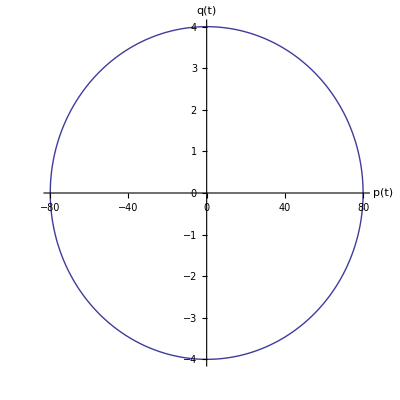

```mathematica
H[q_,p_]:=p^2/(2m)+1/2*m*ω^2 q^2;
(*call the  Hamiltonian Function to get the Ham. Expression.*)
ham=H[q[t],p[t]];
(*Define Hamiltonian Equations..*)
heq1=p'[t]==-D[ham,q[t]];
heq2=q'[t]==D[ham,p[t]];
max=4;(*Solving Hamiltonian Equations..*)
parsol=DSolve[{heq1,heq2,q[0]==max,p[0]==0},{q[t],p[t]},t]
" Extracting functions of p[t], q[t]"
c={p[t],q[t]}/.parsol[[1]]

ParametricPlot[c,{t,0,2Pi/ω},AxesLabel->{"p(t)","q(t)"},AspectRatio->1]
```

```mathematica
??ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions.

Attributes[ParametricPlot]={Protected,ReadProtected}

```mathematica
a=Solve[{x+y==0,2x+3y==4},{x,y}]
{x,y}/.a[[1]]
```

{{x→-4,y→4}}

{-4,4}

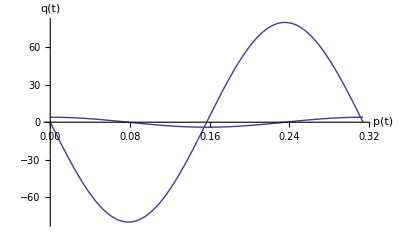

```mathematica
Plot[{p[t],q[t]}/.parsol[[1]],{t,0,2Pi/ω},AxesLabel->{"p(t)","q(t)"}]
```